```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["../lib/lib2.m"];
Get["../lib/util.m"];
```

```mathematica
plotsDir= "./plots";
If[!DirectoryQ[plotsDir], CreateDirectory[plotsDir]];
```

```mathematica
MeanData ={};
VarData ={};
Table[Module[{fn ,data,mns,vars,Kval,tdmns,tdval},
Kval =5;
fn = FileNames[All,"../../runs/Trials/N"<>ToString[Nval]<>"K"<>ToString[Kval]][[1;;3]];
Print[fn];

Print["Computing for N="<>ToString[Nval]];
data =Import[#]&/@fn;

Print["Changing N and K"];
changeNK[Nval,Kval];

matdata = cMat[#]&/@ data;

traces = Table[ Tr[MatrixPower[#, n]]&/@matdata[[d]][[All, 2]]//Chop//Re,{d,1,2},{n,6,8}];
	mnsraw = Table[Mean[traces[[All, k]]], {k, 1, 3}];
(*mnsraw = Table[ Mean[Tr[MatrixPower[#, n]]&/@matdata[[d]][[All, 2]]]//Chop//Re,{n,6,8},{d,1,Length[matdata]}];*)
mns = Around[#]&/@mnsraw;

varsraw = Table[Variance[traces[[All, k]]], {k, 1, 3}];
(*varsraw =Table[ Variance[Tr[MatrixPower[#, n]]&/@matdata[[d]][[All, 2]]]//Chop//Re,{n,6,8},{d,1,Length[matdata]}];*)
vars=  Around[#]&/@varsraw;

tdmns= Thread[{Nval,#}]&/@mns;
tdval = Thread[{Nval,#}]&/@vars;
AppendTo[MeanData,tdmns];
AppendTo[VarData,tdval];

Export["MeanData.mx",MeanData];
Export["VarData.mx",VarData];
Print["Computing COMPLETE for N="<>ToString[Nval]];]
,{Nval,{3,5}}];

Print["Exporting data"];
Export["MeanData.mx",MeanData];
Export["VarData.mx",VarData];
```

{../../runs/Trials/N3K5\37797394.dat,../../runs/Trials/N3K5\37867891.dat,../../runs/Trials/N3K5\43467537.dat}

Computing for N=3

Changing N and K

Computing COMPLETE for N=3

{../../runs/Trials/N5K5\12151246.dat,../../runs/Trials/N5K5\27456936.dat,../../runs/Trials/N5K5\32249329.dat}

Computing for N=5

Changing N and K

Computing COMPLETE for N=5

Exporting data

```mathematica
VarData//Transpose
```

{{{3,0.0020.010},{5,0.00090.0034}},{{3,0.0000.005},{5,0.00020.0012}},{{3,0.0000.005},{5,0.00020.0012}}}

```mathematica
xval ={6,7,8}
```

{6,7,8}

Plotting

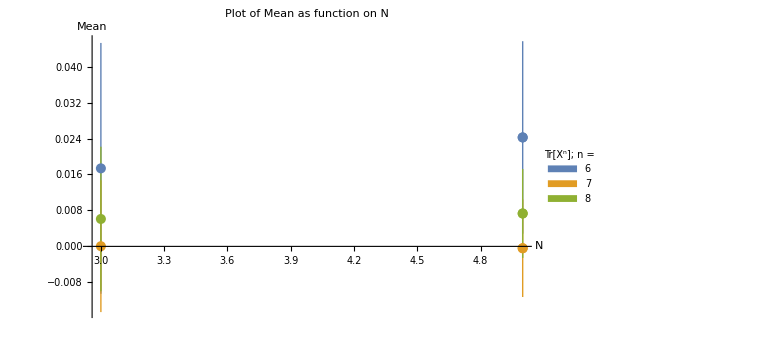

```mathematica
Print["Plotting"];
pltmns = ListPlot[ MeanData//Transpose,PlotLabel->"Plot of Mean as function on N",PlotRange->All,PlotLegends->SwatchLegend[Automatic,xval,LegendLabel->Placed["Tr[\!\(\*SuperscriptBox[\(X\),n]\)]; n = ",Above],LegendFunction->"Frame"],AxesLabel->{"N","Mean"}]
pltvars =ListPlot[ VarData//Transpose,PlotLabel->"Plot of Variance as function on N",PlotLegends->SwatchLegend[Automatic,xval,LegendLabel->Placed["Tr[\!\(\*SuperscriptBox[\(X\),n]\)]; n = ",Above],LegendFunction->"Frame"],AxesLabel->{"N","Variance"}];
```

```mathematica
Print["Exporting Plots"];
Export[plotsDir<>"/Plot_of_Means.pdf",pltmns,ImageResolution->300,ImageSize->500]
Export[plotsDir<>"/Plot_of_Vars.pdf",pltvars,ImageResolution->300,ImageSize->500]
```

```mathematica
Print["Program Completed"];
```